```mathematica
g = 9.8; (*Gravity constant*)
l = 0.5; (*Length of the pendulum*)

θ0 = (20 × π) / 180; (*20 degreen in radians*)
ω0 = 0; (*Starting from rest*)

ode1 = {θ''[t] == - (g/l)*Sin[θ[t]], θ[0] == θ0, θ'[0] == ω0};
sol = NDSolve[ode1, θ, {t, 0, 20}];

myplot1 = Plot[(180/π) θ[t] /. sol, {t, 0, 20}, PlotStyle -> RGBColor[0, 0, 1], PlotRange -> All];

omega = √(g/l);
approx = (180 / π) θ0 Cos[omega * t];
myplot2 = Plot[approx, {t, 0, 20}, PlotStyle -> RGBColor[1, 0, 0], PlotRange -> All];
```

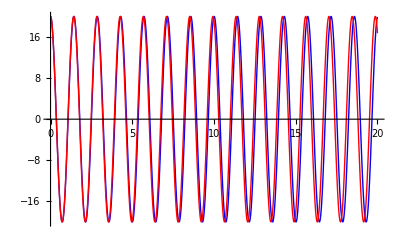

```mathematica
Show[{myplot1, myplot2}]
```

```mathematica
Manipulate[
g = 9.8; l = 0.5; omega = √(g/l);
Module[
{result = NDSolve[{θ''[t] == -(g/l) * Sin[θ[t]], θ[0] == θ0, θ'[0] == ω0}, θ, {t, 0, 20}]},
Plot[{(180 / π) θ0 Cos[omega * t], (180/π) * θ[t] /. result}, {t, 0, 20}, PlotStyle -> {{Blue}, {Dashed, Red}}, PlotRange -> All, AxesLabel -> {"t (s)", "θ (rad)"}, PlotRange -> {{0, 20}, {-20, 20}}, ImageSize -> {500, 300}]],
{{l, 0.5, "Length (m)"}, 0, 2, Appearance -> "Labeled"},
{{θ0, 20 * π/180, "Initial Angle (rad)"}, 0.1, π/2, Appearance -> "Labeled"},
{{ω0, 0, "Initial Speed (rad/s)"}, 0, 10.0, Appearance -> "Labeled"}]
```